```mathematica
a=10;
i = 0;
M1 = 3.2;
M2 = 1.8;
R1 = 2.7;
R2 =1.7;
R3 = 3;
T1 = 13000;
T2= 7500;
T3=5500;
ec = 0;
ϕ=0;
N0=1000;
size=10;
a1=-a*M2/(M1+M2);
a2=a*M1/(M1+M2);
ω = 0;
r[a_,w_,j_]:= (a*(1-w)^2)/(1+w*Cos[ϕ0[j]]);
(*ϕ0[t_]:=Interpolation[Table[{i/N0,ϕ+=(2Pi*1/N0(1+ec*Cos[ϕ])^2)/((1-ec^2)^1.5)},{i,1,N0}]][Mod[t,1]];*)
ϕ0[t_]:=2Pi*t;
(*Grsph[a1_, a2_, R1_, R2_, i_, t_, e_] := Graphics3D[{ {Blue,Sphere[{r[a2,e,t]*Cos[ϕ0[t]+ω*Degree],r[a2,e,t]*Sin[ϕ0[t]+ω*Degree]*Cos[i*Degree],r[a2,e,t]*Sin[ϕ0[t]+ω*Degree]*Sin[i*Degree]},R2 ]},{Red,Sphere[{r[a3,0,t]*Cos[ϕ0[t]+ω*Degree],r[a3,0,t]*Sin[ϕ0[t]+ω*Degree]*Cos[i*Degree],r[a3,0,t]*Sin[ϕ0[t]+ω*Degree]*Sin[i*Degree]},R3 ]}}, PlotRange->{{-2, size}, {-10, 10}, {-10,10}} ,Lighting->{{"Ambient",White}},ViewPoint->{0,-Infinity,0}, Boxed->False, Background->White,ImageSize->800,SphericalRegion->True];*)
Grsph[a1_, a2_, R1_, R2_, t_] := Graphics3D[{ {Blue,Sphere[{a1*Cos[ϕ0[t]],a1*Sin[ϕ0[t]],0},R1 ]},{Red,Sphere[{a2*Cos[ϕ0[t]],a2*Sin[ϕ0[t]],0},R2 ]}}, PlotRange->{{-size, size}, {-size, size}, {-size, size}} ,Lighting->{{"Ambient",White}},ViewPoint->{0,Infinity,0}, Boxed->False, Background->White,ImageSize->800,SphericalRegion->True];


(*Table[Export["/Users/AShepelev/Documents/Light_curve/e=0.6;i=11/e=0.6;i=11_"<>ToString[t]<>".jpg",Grsph[a1,a2,R1,R2,i,t,ec]],{t, 1, 1000, 5}]*)

Grsph[a1,a2,R1,R2,0]
```

-Graphics3D-

```mathematica
curv = Table[{t+ω/360,((T1/T2)^4*Length@PixelValuePositions[Grsph[a1,a2,R1,R2,t], Blue,0.5]+Length@PixelValuePositions[Grsph[a1,a2,R1,R2,t], Red,0.5])}, {t, 0, 1, 0.005}];
```

```mathematica
curvl=Table[{N[curv[[i,1]],7],Round[-2.5Log10[curv[[i,2]]/86176],0.00001]},{i,1,200,1}];
```

```mathematica
TableForm[N[curvl]]
```

0. | 0.
0.005 | -0.00011
0.01 | 0.00021
0.015 | 0.00045
0.02 | -0.00001
0.025 | 0.00034
0.03 | 0.00066
0.035 | -0.00023
0.04 | 0.0009
0.045 | 0.
0.05 | -0.00037
0.055 | 0.00102
0.06 | -0.00013
0.065 | -0.00001
0.07 | 0.00001
0.075 | -0.00001
0.08 | 0.00014
0.085 | -0.00009
0.09 | 0.00057
0.095 | -0.0001
0.1 | -0.00034
0.105 | 0.00014
0.11 | -0.00033
0.115 | -0.00001
0.12 | 0.00004
0.125 | -0.00001
0.13 | 0.00001
0.135 | 0.00002
0.14 | 0.00013
0.145 | 0.00021
0.15 | 0.00019
0.155 | -0.00057
0.16 | -0.00011
0.165 | 0.00015
0.17 | 0.00071
0.175 | 0.00072
0.18 | 0.0049
0.185 | 0.02429
0.19 | 0.05259
0.195 | 0.08861
0.2 | 0.13009
0.205 | 0.1791
0.21 | 0.2329
0.215 | 0.293
0.22 | 0.35693
0.225 | 0.42273
0.23 | 0.48525
0.235 | 0.52014
0.24 | 0.51902
0.245 | 0.51849
0.25 | 0.51888
0.255 | 0.52051
0.26 | 0.51851
0.265 | 0.51851
0.27 | 0.48511
0.275 | 0.42391
0.28 | 0.35663
0.285 | 0.29196
0.29 | 0.23305
0.295 | 0.17844
0.3 | 0.13123
0.305 | 0.08837
0.31 | 0.05242
0.315 | 0.02383
0.32 | 0.00455
0.325 | 0.00013
0.33 | 0.00014
0.335 | 0.00002
0.34 | 0.
0.345 | -0.00001
0.35 | 0.00043
0.355 | 0.
0.36 | 0.00024
0.365 | 0.00037
0.37 | 0.00073
0.375 | -0.00001
0.38 | 0.
0.385 | -0.00014
0.39 | -0.00006
0.395 | 0.00037
0.4 | 0.00101
0.405 | -0.00019
0.41 | -0.00011
0.415 | -0.00044
0.42 | 0.00001
0.425 | 0.00011
0.43 | 0.00014
0.435 | -0.00011
0.44 | -0.00025
0.445 | -0.00023
0.45 | -0.00005
0.455 | 0.00024
0.46 | -0.00024
0.465 | 0.00081
0.47 | -0.00017
0.475 | 0.
0.48 | -0.00013
0.485 | 0.00011
0.49 | 0.00006
0.495 | -0.00058
0.5 | 0.
0.505 | -0.00058
0.51 | 0.00006
0.515 | 0.00011
0.52 | -0.00013
0.525 | 0.
0.53 | -0.00017
0.535 | 0.00081
0.54 | -0.00024
0.545 | 0.00024
0.55 | -0.00005
0.555 | -0.00023
0.56 | -0.00025
0.565 | -0.00011
0.57 | 0.00014
0.575 | 0.00011
0.58 | 0.00001
0.585 | -0.00044
0.59 | -0.00011
0.595 | -0.00019
0.6 | 0.00101
0.605 | 0.00037
0.61 | -0.00006
0.615 | -0.00014
0.62 | 0.
0.625 | -0.00001
0.63 | 0.00073
0.635 | 0.00037
0.64 | 0.00024
0.645 | 0.
0.65 | 0.00043
0.655 | -0.00001
0.66 | 0.
0.665 | 0.00002
0.67 | 0.00014
0.675 | 0.00013
0.68 | 0.00049
0.685 | 0.00274
0.69 | 0.00558
0.695 | 0.00957
0.7 | 0.01469
0.705 | 0.01847
0.71 | 0.02361
0.715 | 0.02863
0.72 | 0.03409
0.725 | 0.04042
0.73 | 0.04412
0.735 | 0.04645
0.74 | 0.04645
0.745 | 0.04764
0.75 | 0.04669
0.755 | 0.04633
0.76 | 0.04657
0.765 | 0.0474
0.77 | 0.0439
0.775 | 0.03928
0.78 | 0.03421
0.785 | 0.02935
0.79 | 0.02348
0.795 | 0.01842
0.8 | 0.01336
0.805 | 0.0098
0.81 | 0.00565
0.815 | 0.00269
0.82 | 0.00074
0.825 | 0.00072
0.83 | 0.00071
0.835 | 0.00015
0.84 | -0.00011
0.845 | -0.00057
0.85 | 0.00019
0.855 | 0.00021
0.86 | 0.00013
0.865 | 0.00002
0.87 | 0.00001
0.875 | -0.00001
0.88 | 0.00004
0.885 | -0.00001
0.89 | -0.00033
0.895 | 0.00014
0.9 | -0.00034
0.905 | -0.0001
0.91 | 0.00057
0.915 | -0.00009
0.92 | 0.00014
0.925 | -0.00001
0.93 | 0.00001
0.935 | -0.00001
0.94 | -0.00013
0.945 | 0.00102
0.95 | -0.00037
0.955 | 0.
0.96 | 0.0009
0.965 | -0.00023
0.97 | 0.00066
0.975 | 0.00034
0.98 | -0.00001
0.985 | 0.00045
0.99 | 0.00021
0.995 | -0.00011

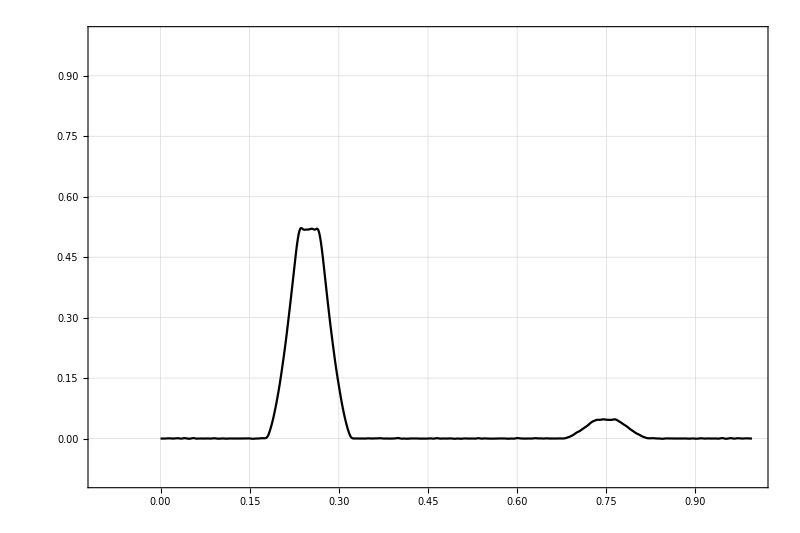

```mathematica
triplecurv=ListPlot[curvl,Joined->True,InterpolationOrder->3,PlotTheme->"Detailed", AspectRatio->1/1.5,FrameStyle->Thickness[Medium],PlotStyle->Black, ImageSize->800,PlotRange->{{-0.1,1},{-0.1,1}}]
```

```mathematica
Export["/Users/AShepelev/Documents/Light_curve/triple_curve.gif",Table[Show[triplecurv,Graphics[{PointSize->0.02,Point[{{ii,Interpolation[curv][ii]}}]},ImageSize->800]]/.ii->i,{i,0, 3, 0.005}]];
```

```mathematica
N[(T2/T1)^4*Length@PixelValuePositions[Grsph[a1,a2,R1,R2,i,0.5, ec], Blue,0.5]+Length@PixelValuePositions[Grsph[a1,a2,R1,R2,i,0.5, ec],Red,0.5]]
```

81517.4

```mathematica
Export["/Users/AShepelev/Desktop/_____d.gif",Table[Grsph[a1,a2,R1,R2,t],{t,0,1,0.01}]]
```

/Users/AShepelev/Desktop/_____d.gif

```mathematica
Animate[Grsph[a1,a2,R1,R2,i,t, ec],{t,0,1,0.01}]
```

```mathematica
Export["/Users/AShepelev/Documents/Light_curve/beta_Per/i17e0.6w135.gif",Table[Grsph[a1,a2,R1,R2,i,t, ec],{t, 0, 1, 0.01}]]
```

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

/Users/AShepelev/Documents/Light_curve/beta_Per/i17e0.6w135.gif

```mathematica
curvetriple = Table[{t,(T2/T1)^4*Length@PixelValuePositions[Grel[a1,a2,R1,R2,i,Mod[t,1000], ec], Blue,0.5]+Length@PixelValuePositions[Grel[a1,a2,R1,R2,i,Mod[t,1000], ec]+(T3/T1)^4,Red,0.5]}
```

```mathematica
a =8;
a1=a*M2/(M1+M2);
a2=a*M1/(M1+M2);
R1 = 4;
R2 =2.5;
Grel[a1_, a2_, R1_, R2_,i_, t_, e_] := Graphics3D[{{Glow[Red],Black,Ellipsoid[{-r[a1,e,t]*Cos[ϕ0[t]],-r[a1,e,t]*Sin[ϕ0[t]]*Cos[i*Degree],-r[a1,e,t]*Sin[ϕ0[t]]*Sin[i*Degree]},{-R1-Abs[Cos[ϕ0[t]]], -R1-Abs[Sin[ϕ0[t]]], R1}] },{Glow[Blue],Black,Ellipsoid[{r[a2,e,t]*Cos[ϕ0[t]],r[a2,e,t]*Sin[ϕ0[t]]*Cos[i*Degree],r[a2,e,t]*Sin[ϕ0[t]]*Sin[i*Degree]},{R2+Abs[Cos[ϕ0[t]]], R2+Abs[Sin[ϕ0[t]]], R2}]}}, PlotRange->{{-size, size}, {-size, size}, {-size, size}} ,ViewPoint->{0,-Infinity,0}, Boxed->False, Background->White, ImageSize->100];
Grsphel[a1_, a2_, R1_, R2_,i_, t_, e_] := Graphics3D[{{Glow[Red],Black,Ellipsoid[{-r[a1,e,t]*Cos[ϕ0[t]],-r[a1,e,t]*Sin[ϕ0[t]]*Cos[i*Degree],-r[a1,e,t]*Sin[ϕ0[t]]*Sin[i*Degree]},{-R1-Abs[Cos[ϕ0[t]]], -R1-Abs[Sin[ϕ0[t]]], R1}] },{Glow[Blue],Black,Sphere[{r[a2,e,t]*Cos[ϕ0[t]],r[a2,e,t]*Sin[ϕ0[t]]*Cos[i*Degree],r[a2,e,t]*Sin[ϕ0[t]]*Sin[i*Degree]},R2 ]}}, PlotRange->{{-size, size}, {-size, size}, {-size, size}} ,ViewPoint->{0,-Infinity,0}, Boxed->False, Background->White, ImageSize->800];

Animate[Grsphel[a1,a2,R1, R2,i,t, ec],{t, 0, 1,0.01}]
(*Table[Export["/Users/AShepelev/Documents/Light_curve/e=0.6;i=11/e=0.6;i=11_"<>ToString[t]<>".jpg",Grsph[a1,a2,R1,R2,i,t,ec]],{t, 1, 1000, 5}]*)
```

```mathematica
curvel=Table[{t,((T2/T1)^4*Length@PixelValuePositions[Grel[a1,a2,R1,R2,i,t, ec], Blue,0.5]+Length@PixelValuePositions[Grel[a1,a2,R1,R2,i,t, ec],Red,0.5])}, {t,0,1, 0.01}];
```

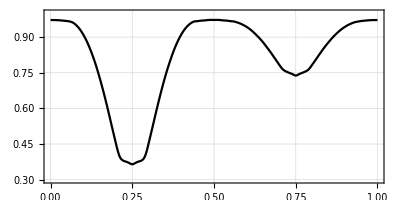

```mathematica
ListPlot[curvel,Joined->True,InterpolationOrder->3,PlotTheme->"Detailed",PlotStyle->RGBColor[0,0,0],AxesStyle->Thick,FrameStyle->Directive[Black,Thickness[Medium]], AspectRatio->1/2,ImageSize->400, PlotRange->{{0,1},{0.3,1}}]
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

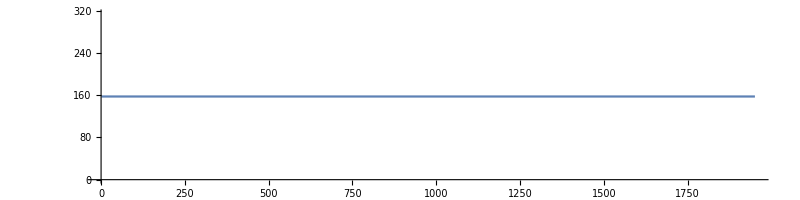

```mathematica
Grelr[a1_, a2_, R1_, R2_,i_, t_, e_] := Graphics3D[{{Glow[Red],Black,Ellipsoid[{-r[a1,e,t]*Cos[ϕ0[t]],-r[a1,e,t]*Sin[ϕ0[t]]*Cos[i*Degree],-r[a1,e,t]*Sin[ϕ0[t]]*Sin[i*Degree]},{R1+2, R1, R1}] },{Glow[Blue],Black,Ellipsoid[{r[a2,e,t]*Cos[ϕ0[t]],r[a2,e,t]*Sin[ϕ0[t]]*Cos[i*Degree],r[a2,e,t]*Sin[ϕ0[t]]*Sin[i*Degree]},{R2+2, R2, R2}]}}, PlotRange->{{-size, size}, {-size, size}, {-size, size}} ,ViewPoint->{0,-Infinity,0}, Boxed->False, Background->White, ImageSize->300];

Animate[Grel[a1,a2,R1, R2,i,t, ec],{t, 1, 1000,20 }]
(*Table[Export["/Users/AShepelev/Documents/Light_curve/e=0.6;i=11/e=0.6;i=11_"<>ToString[t]<>".jpg",Grsph[a1,a2,R1,R2,i,t,ec]],{t, 1, 1000, 5}]*)ListPlot[Table[{t,(T2/T1)^4*Length@PixelValuePositions[Grel[a1,a2,R1,R2,i,Mod[t,1000], ec], Blue,0.5]+Length@PixelValuePositions[Grel[a1,a2,R1,R2,i,Mod[t,1000], ec],Red,0.5]}, {t, 1, 2000, 50}], PlotRange->Full,Joined->True,InterpolationOrder->30,ImageSize->800, AspectRatio->1/4]
```

```mathematica
ϕ=0;
N0=1000;
ec=0.7;
ϕ0[t_]=Interpolation[Table[{i/N0,ϕ+=(2Pi*1/N0(1+ec*Cos[ϕ])^2)/((1-ec^2)^1.5)},{i,1,N0}]][t]
```

InterpolatingFunction[{{0.001, 1.}}, <>][t]

InterpolatingFunction::dmval: Input value {0.0000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

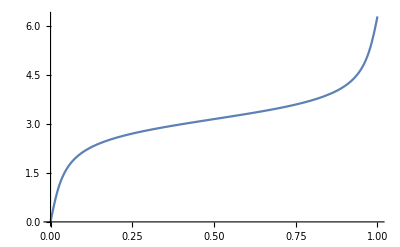

$Aborted

```mathematica
Plot[ϕ0[t],{t,0,1}]
```